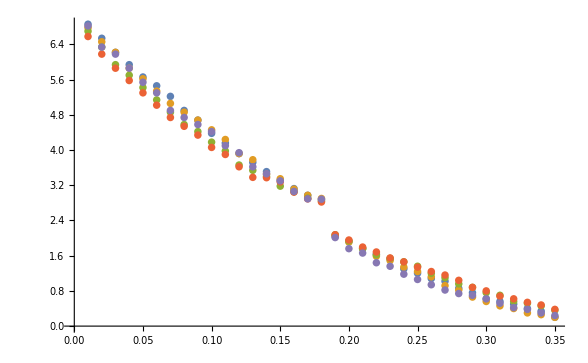

```mathematica
t1step1 =Import ["C:\\Users\\P Wizard\\Documents\\PHY 353L\\Lab 4\\Shared Folder\\T1 min oil Adjusted Amplitudes  - Adjusted Amplitudes .csv"];
t1step2 = Part[%,2;;Length[%]];
t11= Table[{%[[i]][[1]],%[[i]][[2]]+2.5},{i,1,Length[%]}];
t12= Table[{%%[[i]][[1]],%%[[i]][[3]]+2.5},{i,1,Length[%%]}];
t13 =  Table[{%%%[[i]][[1]],%%%[[i]][[4]]+2.5},{i,1,Length[%%%]}];
t14 =  Table[{%%%%[[i]][[1]],%%%%[[i]][[5]]+2.5},{i,1,Length[%%%%]}];
t15 =  Table[{%%%%%[[i]][[1]],%%%%%[[i]][[6]]+2.5},{i,1,Length[%%%%%]}];
ListPlot[{%,%%,%%%,%%%%,%%%%%},AxesLabel->{Time [ms],Voltage[V]}]
```

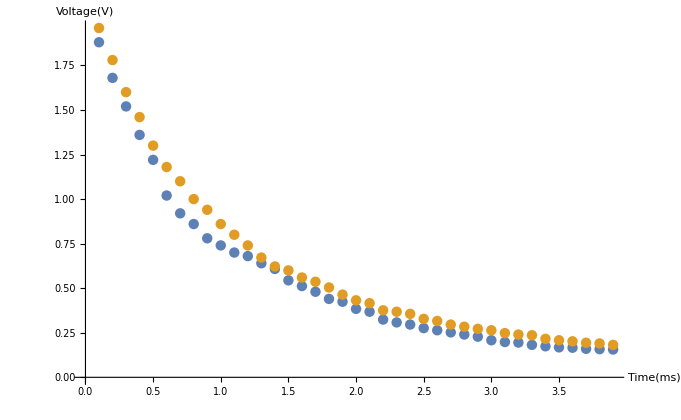

```mathematica
t21step1 = Import ["C:\\Users\\P Wizard\\Documents\\PHY 353L\\Lab 4\\Shared Folder\\T2 min oil .1 step - Sheet1.csv"];
t21step2 = Part[%,2;;Length[%]];
t211= Table[{%[[i]][[1]],%[[i]][[2]]},{i,1,Length[%]-1}];
t212= Table[{%%[[i]][[1]],%%[[i]][[3]]},{i,1,Length[%%]-1}];
ListPlot[{%,%%},AxesLabel->{Time [ms],Voltage[V]}]
```

FittedModel[0.497322-0.610598 x]

0.979429

FittedModel[0.430029-0.648864 x]

0.97934

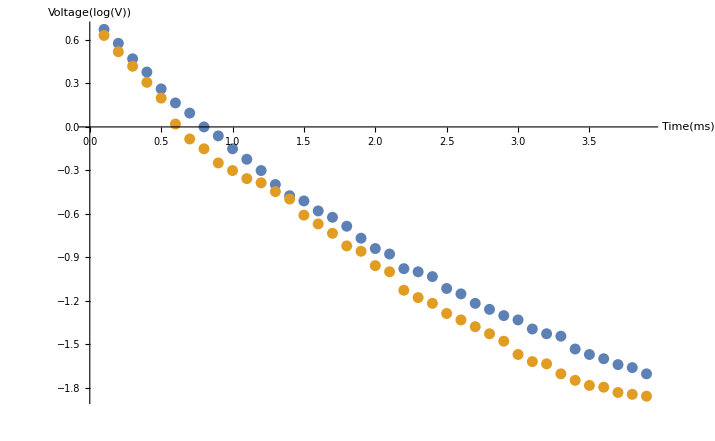

{1.63774,1.54116}

1.58945

0.068295

```mathematica
t211;
t211log =  Table[{%[[i]][[1]],Log[%[[i]][[2]]]},{i,1,Length[%]}];
LinearModelFit[%,{1,x},x]
%["RSquared"]
t212;
t212log =  Table[{%[[i]][[1]],Log[%[[i]][[2]]]},{i,1,Length[%]}];
LinearModelFit[%,{1,x},x]
%["RSquared"]
ListPlot[{t211log,t212log},AxesLabel->{Time [ms],Voltage[Log[V]]}]
T2hs = Table[{-1/-.610598,-1/-.648864}]
Mean[%]
StandardDeviation[%%]
```

0.00163636

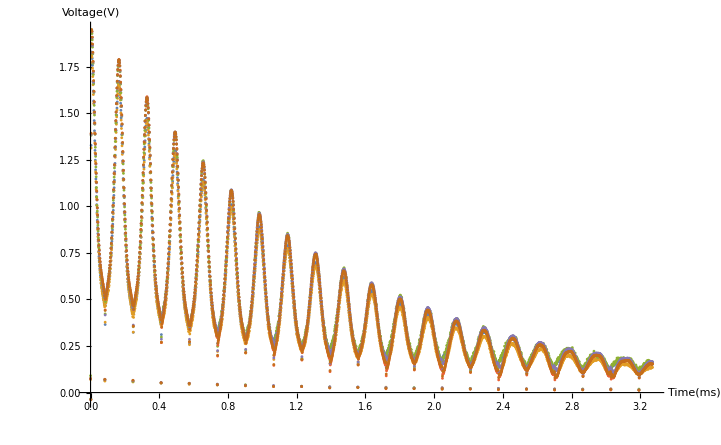

FindPeaks::arg: The argument {{0.,0.0735352},{0.00163636,-0.0354914},{0.00327273,1.32693},{0.00490909,1.75958},{0.00654545,1.82818},{0.00818182,1.81979},{0.00981818,1.7932},{0.0114545,1.75666},{0.0130909,1.71135},«34»,{0.0703636,0.539588},{0.072,0.528479},{0.0736364,0.521122},{0.0752727,0.510685},{0.0769091,0.497856},{0.0785455,0.492068},{0.0801818,0.47954},«1950»} at position 1 is not a consistent list of real values.

```mathematica
cfT2 = 1.8/1100
t221step1 = Import["C:\\Users\\P Wizard\\Documents\\PHY 353L\\Lab 4\\Shared Folder\\07.03.19\\T2_Mineral_1.csv"];
t221step2 = Part[%,2;;Length[%]];
t221 = Table[{%[[i]][[1]]*cfT2 ,%[[i]][[2]]},{i,1,Length[%]}];
t222step1 = Import["C:\\Users\\P Wizard\\Documents\\PHY 353L\\Lab 4\\Shared Folder\\07.03.19\\T2_Mineral_2.csv"];
t222step2 = Part[%,2;;Length[%]];
t222 = Table[{%[[i]][[1]]*cfT2,%[[i]][[2]]},{i,1,Length[%]}];
t223step1 = Import["C:\\Users\\P Wizard\\Documents\\PHY 353L\\Lab 4\\Shared Folder\\07.03.19\\T2_Mineral_3.csv"];
t223step2 = Part[%,2;;Length[%]];
t223 = Table[{%[[i]][[1]]*cfT2,%[[i]][[2]]},{i,1,Length[%]}];
t224step1 = Import["C:\\Users\\P Wizard\\Documents\\PHY 353L\\Lab 4\\Shared Folder\\07.03.19\\T2_Mineral_4.csv"];
t224step2 = Part[%,2;;Length[%]];
t224 = Table[{%[[i]][[1]]*cfT2,%[[i]][[2]]},{i,1,Length[%]}];
t225step1 = Import["C:\\Users\\P Wizard\\Documents\\PHY 353L\\Lab 4\\Shared Folder\\07.03.19\\T2_Mineral_5.csv"];
t225step2 = Part[%,2;;Length[%]];
t225 = Table[{%[[i]][[1]]*cfT2,%[[i]][[2]]},{i,1,Length[%]}];
t226step1 = Import["C:\\Users\\P Wizard\\Documents\\PHY 353L\\Lab 4\\Shared Folder\\07.03.19\\T2_Mineral_6.csv"];
t226step2 = Part[%,2;;Length[%]];
t226 = Table[{%[[i]][[1]]*cfT2,%[[i]][[2]]},{i,1,Length[%]}];
ListPlot[{t221,t222,t223,t224,t225,t226},AxesLabel->{Time [ms],Voltage[V]}]
t221;
t221peaksfix = Table[{%[[i]][[2]]},{i,1,Length[%]}];
FindPeaks[%%,0,0,-∞];
```

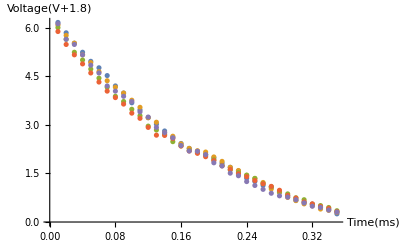

FittedModel[2.09183-8.26341 x]

0.973005

FittedModel[1.99113-7.60597 x]

0.965252

FittedModel[2.00345-7.5491 x]

0.970668

FittedModel[2.11909-8.21078 x]

0.954984

FittedModel[2.11605-8.17624 x]

0.958832

{0.121015,0.131476,0.132466,0.121791,0.122306}

0.125811

0.00565297

```mathematica
t12step1 =Import ["C:\\Users\\P Wizard\\Documents\\PHY 353L\\Lab 4\\Shared Folder\\t1_2_adjustment.csv"];
t12step2 = Part[%,42;;Length[%]];
t112= Table[{%[[i]][[1]],%[[i]][[2]]},{i,1,Length[%]}];
t122= Table[{%%[[i]][[1]],%%[[i]][[3]]},{i,1,Length[%%]}];
t132 =  Table[{%%%[[i]][[1]],%%%[[i]][[4]]},{i,1,Length[%%%]}];
t142 =  Table[{%%%%[[i]][[1]],%%%%[[i]][[5]]},{i,1,Length[%%%%]}];
t152 =  Table[{%%%%%[[i]][[1]],%%%%%[[i]][[6]]},{i,1,Length[%%%%%]}];
ListPlot[{%,%%,%%%,%%%%,%%%%%},AxesLabel->{Time [ms],Voltage[V+1.8]}]
t112;
t112log = Table[{%[[i]][[1]],Log[%[[i]][[2]]]},{i,1,Length[%]}];
LinearModelFit[%,{1,x},x]
%["RSquared"]
t122;
t122log= Table[{%[[i]][[1]],Log[%[[i]][[2]]]},{i,1,Length[%]}];
LinearModelFit[%,{1,x},x]
%["RSquared"]
t132;
t132log =  Table[{%[[i]][[1]],Log[%[[i]][[2]]]},{i,1,Length[%]}];
LinearModelFit[%,{1,x},x]
%["RSquared"]
t142;
t142log =  Table[{%[[i]][[1]],Log[%[[i]][[2]]]},{i,1,Length[%]}];
LinearModelFit[%,{1,x},x]
%["RSquared"]
t152;
t152log =  Table[{%[[i]][[1]],Log[%[[i]][[2]]]},{i,1,Length[%]}];
LinearModelFit[%,{1,x},x]
%["RSquared"]
ListPlot[{t112log,t122log,t132log,t142log,t152log},AxesLabel->{Time [ms],Voltage[Log[V+1.8]]}];
T2hs = Table[{-1/-8.26341,-1/-7.60597,-1/-7.5491,-1/-8.21078,-1/-8.17624}]
Mean[%]
StandardDeviation[%%]
```

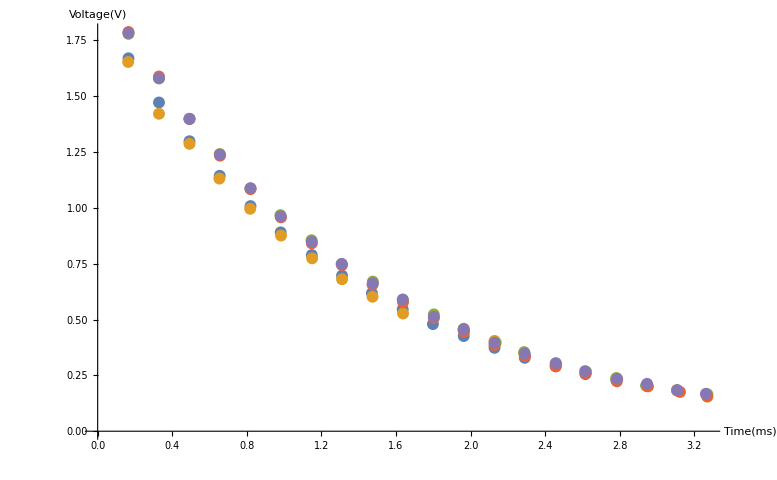

```mathematica
t231step1 = Import["C:\\Users\\P Wizard\\Documents\\PHY 353L\\Lab 4\\Shared Folder\\07.03.19\\T2_Mineral_1 envelope.csv"];
t231step2 = Part[%,2;;Length[%]];
t231 = Table[{%[[i]][[1]]*cfT2,%[[i]][[2]]},{i,1,Length[%]}];
t232step1 = Import["C:\\Users\\P Wizard\\Documents\\PHY 353L\\Lab 4\\Shared Folder\\07.03.19\\T2_Mineral_2 envelope.csv"];
t232step2 = Part[%,2;;Length[%]];
t232 = Table[{%[[i]][[1]]*cfT2,%[[i]][[2]]},{i,1,Length[%]}];
t23step1 = Import["C:\\Users\\P Wizard\\Documents\\PHY 353L\\Lab 4\\Shared Folder\\07.03.19\\T2_Mineral_3 envelope.csv"];
t233step2 = Part[%,2;;Length[%]];
t233 = Table[{%[[i]][[1]]*cfT2,%[[i]][[2]]},{i,1,Length[%]}];
t234step1 = Import["C:\\Users\\P Wizard\\Documents\\PHY 353L\\Lab 4\\Shared Folder\\07.03.19\\T2_Mineral_4 envelope.csv"];
t234step2 = Part[%,2;;Length[%]];
t234 = Table[{%[[i]][[1]]*cfT2,%[[i]][[2]]},{i,1,Length[%]}];
t235step1 = Import["C:\\Users\\P Wizard\\Documents\\PHY 353L\\Lab 4\\Shared Folder\\07.03.19\\T2_Mineral_5 envelope.csv"];
t235step2 = Part[%,2;;Length[%]];
t235 = Table[{%[[i]][[1]]*cfT2,%[[i]][[2]]},{i,1,Length[%]}];
ListPlot[{t231,t232,t233,t234,t235},AxesLabel->{Time [ms],Voltage[V]}]
```

```mathematica
t231;
t231log =  Table[{%[[i]][[1]],Log[%[[i]][[2]]]},{i,1,Length[%]}];
LinearModelFit[%,{1,x},x]
%["RSquared"]
t232;
t232log =  Table[{%[[i]][[1]],Log[%[[i]][[2]]]},{i,1,Length[%]}];
LinearModelFit[%,{1,x},x]
%["RSquared"]
t233;
t233log =  Table[{%[[i]][[1]],Log[%[[i]][[2]]]},{i,1,Length[%]}];
LinearModelFit[%,{1,x},x]
%["RSquared"]
t234;
t234log =  Table[{%[[i]][[1]],Log[%[[i]][[2]]]},{i,1,Length[%]}];
LinearModelFit[%,{1,x},x]
%["RSquared"]
t235;
t235log =  Table[{%[[i]][[1]],Log[%[[i]][[2]]]},{i,1,Length[%]}];
LinearModelFit[%,{1,x},x]
%["RSquared"]
ListPlot[{t231log,t232log,t233log,t234log,t235log},AxesLabel->{Time [ms],Voltage[Log[V]]}];
T2hs = Table[{-1/-0.753215,-1/-0.740761,-1/-0.776135,-1/-0.792195,-1/-0.771814}]
Mean[%]
StandardDeviation[%%]
```

FittedModel[0.627018-0.753215 x]

0.999786

FittedModel[0.608981-0.740761 x]

0.998354

FittedModel[0.724298-0.776135 x]

0.999608

FittedModel[0.73153-0.792195 x]

0.999731

FittedModel[0.717897-0.771814 x]

0.999831

{1.32764,1.34996,1.28844,1.26232,1.29565}

1.3048

0.0343436